# Run ILOCI v 0.9 Simulated with no mcp3008

Modified 10/27/16 to add HALT command “sudo halt”, to rfcomm argument list.  Command is implemented using CMD2

#### Give the file path and name of the classifier to be used

```mathematica
csvfilepath="~/Mathematica/";
```

```mathematica
classifierfile = csvfilepath <> "ILOCITest7Classifier.m";
```

#### Give the name of the ILOCI training file that was first used, to be updated

```mathematica
trainingfile=csvfilepath<>"ILOCITrainingFile.m"
```

~/Mathematica/ILOCITrainingFile.m

#### Load the SPI analog data Mathlink

```mathematica
linkmcp3008 = Install["/home/pi/projects/ML_spidev_mcp3008/ML_spidev_mcp3008"]
```

LinkObject[…]

#### Specify data recording parameters

```mathematica
nchannels=8;frametime=0.2;
(*dt=frametime*10^*6 -2200 *)
dt = Floor[frametime*1000000-2000]; (*SPIDevMcp3008 requires an integer parameter*)(*200 mseconds is the goal but we subtract a 2 msec for the program overhead*)
```

#### Load the Bluetooth rfcomm Mathlink

```mathematica
linkrfcomm = Install["/home/pi/projects/ML_System/ML_System"]
```

LinkObject[…]

#### Initialize the classify method

```mathematica
nchannels=8;frametime=0.2;
```

```mathematica
classify = Get[classifierfile]
```

ClassifierFunction[…]

#### Initialize rfcomm to add Bluetooth channel 22

```mathematica
{RFCOMMINIT = 0,CONNECT= 1,LISTEN=2, HANGUP = 3,SHOW = 4, PYTHON = 5, HALT = 6};
```

```mathematica
rfcomm[RFCOMMINIT];
```

## Essential Functions

### Initialization and Log file functions

```mathematica
d=Date[];
 logname= "/home/pi/Mathematica/runnumber.log";
 lognumber=Import[logname,"List"][[1]];
 lognumber = lognumber +1;
 Export[logname,lognumber,"List"];
```

#### Create a file name to hold all the real time saved ILOCI events

```mathematica
updatefilename= "/home/pi/Mathematica/"<>ToString[d[[1]]]<>"_"<>ToString[d[[2]]]<>"_"<>ToString[d[[3]]]<>"_"<>ToString[lognumber]<>".m"
```

/home/pi/Mathematica/2017_4_21_192.m

#### Create the data recording file name and open a handle for writing (which must be closed before terminating the session)

```mathematica
datename= "/home/pi/Mathematica/"<>ToString[d[[1]]]<>"_"<>ToString[d[[2]]]<>"_"<>ToString[d[[3]]]<>"_"<>ToString[lognumber]<>".dat";
Print["datename File is ",datename];
datafilehandle = OpenWrite[datename];
```

datename File is /home/pi/Mathematica/2017_4_21_192.dat

#### Name a log file to record events

```mathematica
logfilename= "/home/pi/Mathematica/"<>ToString[d[[1]]]<>"_"<>ToString[d[[2]]]<>"_"<>ToString[d[[3]]]<>"_"<>ToString[lognumber]<>"_log.txt";
PutAppend[DateString[]<>":Start",logfilename];
```

### Classifier helper functions

#### Define rules to extract probabilities for each class

```mathematica
pN=classify[#,"Probabilities"][[3]]&;
```

```mathematica
pD=classify[#,"Probabilities"][[1]]&;
```

```mathematica
pL=classify[#,"Probabilities"][[2]]&;
```

```mathematica
pR=classify[#,"Probabilities"][[4]]&;
```

classify[realdata[[1]], "Probabilities"]

<|"D"→1.33323×10^-130,"L"→8.87982×10^-89,"N"→1.,"R"→7.59543×10^-87|>

#### Check the data is accessible using SPI

```mathematica
SPIDevMcp3008[nchannels,0]
```

{0,0,0,0,0,0,0,0,1492813999,505845}

#### Use a function to read the SPI data, and condition it if necessary. Keep the last few frames in a list called realdata, and write each frame to the log file

The data rate is roughly one measurement every 0.2 secs, or 5 Hz.  This is about as fast as the RPi2 can handle

```mathematica
GetOneFrame[]:=Module[{linelist,adc},realdata={};
adc=SPIDevMcp3008[nchannels,dt];
(*write the list to the log file handle s*)
  WriteString[datafilehandle,adc[[1]]," ",adc[[2]]," ",adc[[3]]," ",adc[[4]]," ",adc[[5]]," ",adc[[6]]," ",adc[[7]]," ",adc[[8]],"\n"];
(* write the list to a list realdata for use by classify. More than one frame can be added if classify looks at data history (derivatives) *)
linelist={adc[[1]],adc[[2]],adc[[3]],adc[[4]],adc[[5]],adc[[6]],adc[[7]],adc[[8]]};
AppendTo[realdata,linelist];
nframes=nframes +1; (*so we know how many frames, for time measurements*)
];
```

```mathematica
nframes=0;
```

#### showOneFramePerformance returns a list of 4 values, each being the probability of the classes N, D, L, R

Choose a threshold value for the action probabilities by setting paction

```mathematica
(*showOneFramePerformance runs classify by applyin the probability rules*)
showOneFramePerformance[printQ_]:=Module[{probN,probD,probL,probR,paction},
probN=Part[pN/@realdata,1];
If[probN < 0.0001,probN=0.];(*make really small numbers zero*)
probD=Part[pD/@realdata,1];
If[probD < 0.0001,probD=0.];(*make really small numbers zero*)
probL=Part[pL/@realdata,1];
If[probL < 0.0001,probL=0.];(*make really small numbers zero*)
probR=Part[pR/@realdata,1];
If[probR < 0.0001,probR=0.];(*make really small numbers zero*)
(*add a leading digit to probN based on the action required*)
paction=0.5;
If[probD > paction,probN=probN+2.0];
If[probL > paction,probN=probN+3.0];
If[probR > paction,probN=probN+4.0];
{probN,probD,probL,probR}];
```

```mathematica
GetOneFrame[];realdata
```

{{0,0,0,0,0,0,0,0}}

```mathematica
showOneFramePerformance[False]
```

{1.,0.,0.,0.}

#### Create realistic data for ILOCI sitting on the bench

this is data during a straight stall during Test 7

ListLinePlot[Transpose[{{510, 598, 508, 517, 171, 755, 469, 755}, {507, 613, 508, 517, 174, 745, 460, 755}, {509, 609, 504, 515, 173, 739, 416, 756}, {508, 604, 537, 509, 178, 536, 435, 758}, {512, 591, 512, 507, 190, 528, 393, 789}, {515, 590, 503, 506, 194, 662, 481, 803}, {513, 611, 511, 507, 196, 550, 313, 801}, {514, 599, 485, 525, 194, 835, 316, 769}, {515, 615, 506, 505, 183, 457, 543, 806}, {520, 579, 510, 328, 174, 619, 504, 805}, {520, 566, 513, 291, 173, 810, 433, 745}}]]

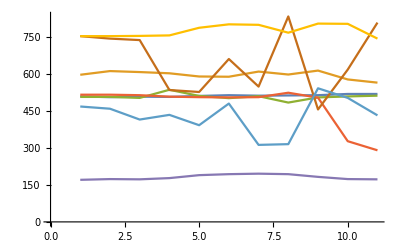

```mathematica
tableTopILOCI[]:=Module[{real,flight,flighttable,lt},
real=realdata[[1]];(*will be all zeros if no mcp3008*)
flighttable = {{510,598,508,517,171,755,469,755},{507,613,508,517,174,745,460,755},{509,609,504,515,173,739,416,756},{508,604,537,509,178,536,435,758},{512,591,512,507,190,528,393,789},{515,590,503,506,194,662,481,803},{513,611,511,507,196,550,313,801},{514,599,485,525,194,835,316,769},{515,615,506,505,183,457,543,806},{520,579,510,328,174,619,504,805},{520,566,513,291,173,810,433,745}};
lt=Length[flighttable];
flight=flighttable[[RandomInteger[{1,lt}]]];
table=real;(*{512,606,511,507,504,179,124,388};*)
realdata={flight-table+real}
]
```

```mathematica
tableTopILOCI[]
```

{{509,609,504,515,173,739,416,756}}

### RFComm functions

```mathematica
rfcommConnect[t_]:= Module[{singleread,time,timeout,goodQ},
goodQ=False;(*keep track of what has worked during the connection process*)
DeviceClose[commdev];(*Hanup our last event, if it was not done previously*)
rfcomm[HANGUP];
timeout = t;time=0;
While[rfcomm[SHOW]== 0, (*returns 1 when connected*)
(*creates a serial device linked to the bluetooth serial channel 22*)
 rfcomm[CONNECT];(*not a blocking call*)
Pause[1];(*wait until the connection is made*)
time = time + 1;(*increment our timeout clock*)
If[time > timeout,
Print["Make connection time out. Hanging up"];
DeviceClose[commdev];
rfcomm[HANGUP];
Break[]
];
goodQ= True;
];
(*verify we are connected*)
If[FileExistsQ["/dev/rfcomm0"],(*this is proof from linux we are connected*)
Print["Connected to client"];
commdev=DeviceOpen["Serial","/dev/rfcomm0"];
goodQ=True,(*so this is Mathematica's access to the serial port*)
(*else*)
Print["/dev/rfcomm0 was not created as expected"];
DeviceClose[commdev];
rfcomm[HANGUP];
goodQ=False;
];
(*receive a response from the listener*)
While[!DeviceExecute[commdev,"SerialReadyQ"],
Pause[1];
If[rfcomm[SHOW]==0,Break[];goodQ=False](*keep checking to see if the connection was dropped*)
];
If[rfcomm[SHOW]==1,
(*the response should be terminated with a new line character byte \n, which is 10 decimal*)
singleread= FromCharacterCode[DeviceReadBuffer[commdev,"ReadTerminator"->10]],
(*else*)
Print["Connection was dropped"];goodQ=False
];
(*verify what we got was "Ready for data"*)
If[singleread == "Ready for data",
DeviceWrite[commdev,"data follows\n"];goodQ=True,
(*else*)
Print["Unexpected response from the client..Hanging up"];
PutAppend[DateString[]<>":Unexpected response from the client..Hanging up",logfilename];
DeviceClose[commdev];
rfcomm[HANGUP];
goodQ=False;
];
goodQ
];
```

#### Sending float values

```mathematica
(*sendFloat[f_]:=Module[{goodQ,trys,singleread,x},
goodQ=False;
trys=0;
(*prevent display of f in MMA scientific notation
as the Python float function cannot read it *)
x=FortranForm[SetPrecision[f,5]];
DeviceWrite[commdev,ToString[x]<>"\n"];
While[trys <  250,(* a second or so wait*)
If[DeviceExecute[commdev,"SerialReadyQ"],
singleread= DeviceReadBuffer[commdev,"ReadTerminator"->10];
(*Print["recvd ",ToExpression[singleread]]*)
If[Length [singleread]==0,
goodQ=True;
Break[];
];
];
trys = trys+1;
];
goodQ
];*)

sendFloatReceiveCommand[f_]:=Module[{goodQ,trys,singleread,x},
goodQ=False;
trys=0;
(*prevent display of f in MMA scientific notation
as the Python float function cannot read it *)
x=FortranForm[SetPrecision[f,5]];
DeviceWrite[commdev,ToString[x]<>"\n"];
While[trys <  10000,(* a 20 second or so wait*)
If[DeviceExecute[commdev,"SerialReadyQ"],
singleread= DeviceReadBuffer[commdev,"ReadTerminator"->10];
(*Print["recvd ",ToExpression[singleread]]*)
If[Length [singleread]>=0,
goodQ=True;
receivedCommand= FromCharacterCode[singleread];
Break[];
];
];
trys = trys+1;
];
goodQ
];
```

#### process Commands

```mathematica
(*Process the commands from the two lbuttons of the listener*)
(*changes made to processCommand v2.2 2/19/16 -cmf*)
processCommand[]:=Module[{result},
 If[StringLength[receivedCommand]>0,
    Print["Received command "<> receivedCommand];
    PutAppend[DateString[]<>":Received command "<>receivedCommand,logfilename];
 ];
 Switch[receivedCommand,
"CMD1",saveUpdatePairs[],
         "CMD2",Print["Exiting.. for CMD2"];
             PutAppend[DateString[]<>":Exiting ",logfilename];
stopsending=True;
rfcomm[HALT],
,
"CMD3",Print["pauseSending[30] not implemented"]
   ];
];
```

```mathematica
(*pauseSending[delay_]:=Module[{trys,singleread},
(*DeviceWrite[commdev,ToString[f]<>"\n"];*)
Do[(* a delay second or so wait*)
If[DeviceExecute[commdev,"SerialReadyQ"],
singleread= DeviceReadBuffer[commdev,"ReadTerminator"->10];
If[Length [singleread]>=0,
receivedCommand= FromCharacterCode[singleread];
Print["pauseSending received ",receivedCommand];
(*Return[];*)
];
],
{i,1,250*delay}
];
sendFloatReceiveCommand[8881.0];(*a code for CMD3 timedout*)
Print["pauseSending timedout "];
]*)
```

#### Initialize Update functions for training data lists

```mathematica
(*Setup the update pair list*)
(*as determined by the listener display horizontal pixel count*)listenerdisplaypoints = 120;(*needs to be defined in one place*)
ILOCIperiod = 10.0; (*time in seconds used to create an ILOCI training rule set*)
nupdates = ILOCIperiod/frametime;updatedata = {};(*a global list containing recent measurements for additional training*)
```

```mathematica
(**)
AddDataToUpdate[]:=Module[{},
If[Length[updatedata]>=nupdates,
(*remove the first measurement in the list, the oldest one*)
updatedata= Take[updatedata,-(nupdates-1)];
];
AppendTo[updatedata,realdata[[1]]];
];
```

#### Saving the update data as a reduced data table for post flight inspection and training

```mathematica
(*saveUpdatePairs is called by processCommands *)
saveUpdatePairs[]:=Module[{existing,newupdates},
If[FileExistsQ[updatefilename],
existing = Import[updatefilename];
         newupdates =Join[existing,updatedata];
Put[newupdates,updatefilename];,
(*else*)
Put[updatedata,updatefilename];
];
 Print["Appended update data to "<>updatefilename];
 PutAppend[DateString[]<>":Appended update data to "<>updatefilename,logfilename];
];
```

## Get a data frame to classify

#### Setup the update pair list

```mathematica
Dynamic[Length[updatedata]]
```

test ..

```mathematica
GetOneFrame[];
tableTopILOCI[];pN/@realdata
```

{0.971739}

#### Display what we are sending to the listener

```mathematica
probabilities={};
Do[AppendTo[probabilities,0],{i,1,listenerdisplaypoints}];
```

```mathematica
Dynamic[ListPlot[probabilities,Frame->True,GridLines->Automatic,Joined->True,PlotRange->{{0,listenerdisplaypoints},{0,5}}]]
```

```mathematica
stopsending= False;
Button["Stop Sending",stopsending=True]
```

Stop Sending

```mathematica
Dynamic[OOF]
```

#### Run the ILOCI main loop

```mathematica
rfcommConnect[3600]
```

DeviceClose::ncdev: commdev is not open.

Connected to client

True

```mathematica
(*;*)
stopsending= False;
While[!stopsending,
If[rfcomm[SHOW]==0,
   Print["connection dropped - hanging up"];
   PutAppend[DateString[]<>":Connection dropped - hanging up!",logfilename];
   Break[];
  ];
  GetOneFrame[];(*get a data frames in a list called realdata*)
 (*the next line is for table top ILOCI only*)
 tableTopILOCI[];(*comment this out. NOT FOR FLIGHT*)
  output=showOneFramePerformance[False];

  AddDataToUpdate[];
  OOF=output[[1]];

  commQ = sendFloatReceiveCommand[OOF];
  If[!commQ,
   Print["comm dropped.."];
   PutAppend[DateString[]<>":Comm dropped!",logfilename];
   Break[];
  ];

  processCommand[];
probabilities = Take[probabilities,-(listenerdisplaypoints-1)];
AppendTo[probabilities,OOF];
];
DeviceClose[commdev];
rfcomm[HANGUP];
```

Switch::argct: Switch called with 8 arguments. Switch must be called with an odd number of arguments.

General::stop: Further output of Switch :: argct will be suppressed during this calculation.

#### Close Devices (when running as a script)

```mathematica
DeviceClose[commdev];
rfcomm[HANGUP];
```

DeviceObject::ncdev: … is not open.

```mathematica
Close[datafilehandle]
```

/home/pi/Mathematica/2016_6_26_115.dat

```mathematica
Uninstall[linkrfcomm]
```

'/home/pi/projects/ML_System/ML_System'

```mathematica
Uninstall[linkmcp3008]
```

'/home/pi/projects/ML_spidev_mcp3008/ML_spidev_mcp3008'